## SE 267A HW2

## Problem 1

```mathematica
(* Define the original analog signal and calculate its properties. *)
Print[Style["Angular frequency Ω_i (rad/s) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Omega = {2000π, 6000π, 12000π, 15000π, 20000π}

Print[Style["Fundamental frequency f_pi (Hz) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Frequency = Omega/(2π)

Print[Style["Fundamental period T_pi (s) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Period = 1/Frequency

Print[Style["Amplitude A_i for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Amplitude = {1, 5, 10, 20, 10}

Print[Style["Phase difference Φ_i (rad) for each harmonic signal:", Bold, FontFamily->"Times", FontSize->14]]
Phi = {0, -π/2, 0, 0, -π/2}

f1 = Amplitude[[1]] * Cos[Omega[[1]]*t + Phi[[1]]];
f2 = Amplitude[[2]] * Cos[Omega[[2]]*t + Phi[[2]]];
f3 = Amplitude[[3]] * Cos[Omega[[3]]*t + Phi[[3]]];
f4 = Amplitude[[4]] * Cos[Omega[[4]]*t + Phi[[4]]];
f5 = Amplitude[[5]] * Cos[Omega[[5]]*t + Phi[[5]]];

Print[Style["Original analog signal: ", Bold, FontFamily->"Times", FontSize->14],Style["f(t)", Italic, Bold, FontFamily->"Times", FontSize->14]]
f = f1+f2+f3+f4+f5;
f/.Sin[var_]:>HoldForm[Cos[var-π/2]]

(* Calculate the fundamental time period of the original analog signal. *)
Print[Style["The fundamental time period T_p (second) of the original analog signal:", Bold, FontFamily->"Times", FontSize->14]]
Tp = LCM[Period[[1]], Period[[2]], Period[[3]], Period[[4]], Period[[5]]]

(* Calculate the intergration for Dirichlet conditions of convergence. *)
Print[Style["Integration result for Dirichlet conditions of convergence:", Bold, FontFamily->"Times", FontSize->14]]
NIntegrate[Abs[f], {t, -Tp/2, Tp/2}]
```

Angular frequency Ω_i (rad/s) for each harmonic signal:

{2000 π,6000 π,12000 π,15000 π,20000 π}

Fundamental frequency f_pi (Hz) for each harmonic signal:

{1000,3000,6000,7500,10000}

Fundamental period T_pi (s) for each harmonic signal:

{1/1000,1/3000,1/6000,1/7500,1/10000}

Amplitude A_i for each harmonic signal:

{1,5,10,20,10}

Phase difference Φ_i (rad) for each harmonic signal:

{0,-π/2,0,0,-π/2}

Original analog signal: f(t)

Cos[2000 π t]+10 Cos[12000 π t]+20 Cos[15000 π t]+5 Cos[6000 π t-π/2]+10 Cos[20000 π t-π/2]

The fundamental time period T_p (second) of the original analog signal:

1/500

Integration result for Dirichlet conditions of convergence:

0.029185

The function is absolutely integrable over its fundamental period. Also, this is a continuous function and it contains a finite number of maximum and minimum values over its fundamental period. So Dirichlet conditions of convergence hold for this function. The Fourier coefficients exist and the function can be represented by Fourier series.

## Problem 2

```mathematica
(* Calculate the fundamental frequency of the original analog signal. *)
Print[Style["The fundamental frequency f_p (Hz) of the original analog signal:", Bold, FontFamily->"Times", FontSize->14]]
fp = 1/Tp

(* Obtain the maximum frequency of the original analog signal. *)
Print[Style["The maximum frequency f_(p, max) (Hz) of the original analog signal:", Bold, FontFamily->"Times", FontSize->14]]
MaxFrequency = Max[Frequency]

(* Calculate the maximum index for the exact representation using Fourier series. *)
Print[Style["The maximum index m_max for the exact representation using Fourier series:", Bold, FontFamily->"Times", FontSize->14]]
MaxIndex = MaxFrequency/fp
```

The fundamental frequency f_p (Hz) of the original analog signal:

500

The maximum frequency f_(p, max) (Hz) of the original analog signal:

10000

The maximum index m_max for the exact representation using Fourier series:

20

## Problem 3

```mathematica
m = Range[1,MaxIndex]; (* Index for the harmonics in the Fourier serires. *)
fm = m*fp; (* Frequency. *)
OmegaM = 2π*fm; (* Angular frequency. *)
Fm = Integrate[f*Exp[-I*OmegaM*t], {t, -Tp/2, Tp/2}]/Tp; (* Fourier coefficients. *)
FmMagnitude = Abs[Fm]; (* Magnitude of Fourier coefficients. *)
theta = Arg[Fm]; (* Phase of Fourier coefficients. *)
PowerDensity = FmMagnitude^2; (* Power dentsity spectrum. *)

(* List a table for the Fourier coefficients. *)
Title = {"Harmonic index m", "Frequency f_m", "Angular frequency Ω_m", "Magnitude |F_m|", "Phase θ_m ", "Power density spectrum", "Fourier coefficient F_m"};
Data = Transpose[{m, fm, OmegaM, FmMagnitude, theta, PowerDensity, Fm}];
AppendData = Prepend[Data, Title];
StyledData = Map[Style[#, FontFamily->"Times", FontSize->8, FontWeight->Bold] &, AppendData, {2}];
Grid[StyledData, Frame->All, ItemSize->{8, 1}, Alignment->Center]
```

Harmonic index m | Frequency f_m | Angular frequency Ω_m | Magnitude |F_m| | Phase θ_m  | Power density spectrum | Fourier coefficient F_m
1 | 500 | 1000 π | 0 | 0 | 0 | 0
2 | 1000 | 2000 π | 1/2 | 0 | 1/4 | 1/2
3 | 1500 | 3000 π | 0 | 0 | 0 | 0
4 | 2000 | 4000 π | 0 | 0 | 0 | 0
5 | 2500 | 5000 π | 0 | 0 | 0 | 0
6 | 3000 | 6000 π | 5/2 | -π/2 | 25/4 | -(5 ⅈ)/2
7 | 3500 | 7000 π | 0 | 0 | 0 | 0
8 | 4000 | 8000 π | 0 | 0 | 0 | 0
9 | 4500 | 9000 π | 0 | 0 | 0 | 0
10 | 5000 | 10000 π | 0 | 0 | 0 | 0
11 | 5500 | 11000 π | 0 | 0 | 0 | 0
12 | 6000 | 12000 π | 5 | 0 | 25 | 5
13 | 6500 | 13000 π | 0 | 0 | 0 | 0
14 | 7000 | 14000 π | 0 | 0 | 0 | 0
15 | 7500 | 15000 π | 10 | 0 | 100 | 10
16 | 8000 | 16000 π | 0 | 0 | 0 | 0
17 | 8500 | 17000 π | 0 | 0 | 0 | 0
18 | 9000 | 18000 π | 0 | 0 | 0 | 0
19 | 9500 | 19000 π | 0 | 0 | 0 | 0
20 | 10000 | 20000 π | 5 | -π/2 | 25 | -5 ⅈ

## Problem 4

```mathematica
m = Range[-30,30]; (* Index for the harmonics in the Fourier serires. *)
fm = m*fp; (* Frequency. *)
OmegaM = 2π*fm; (* Angular frequency. *)
Fm = Integrate[f*Exp[-I*OmegaM*t], {t, -Tp/2, Tp/2}]/Tp; (* Fourier coefficients. *)
FmMagnitude = Abs[Fm]; (* Magnitude of Fourier coefficients. *)
theta = Arg[Fm]; (* Phase of Fourier coefficients. *)
PowerDensity = FmMagnitude^2; (* Power dentsity spectrum. *)

(* List a table for the Fourier coefficients. *)
Title = {"Harmonic index m", "Frequency f_m", "Angular frequency Ω_m", "Magnitude |F_m|", "Phase θ_m ", "Power density spectrum", "Fourier coefficient F_m"};
Data = Transpose[{m, fm, OmegaM, FmMagnitude, theta, PowerDensity, Fm}];
AppendData = Prepend[Data, Title];
StyledData = Map[Style[#, FontFamily->"Times", FontSize->8, FontWeight->Bold] &, AppendData, {2}];
Grid[StyledData, Frame->All, ItemSize->{8, 1}, Alignment->Center]
```

Harmonic index m | Frequency f_m | Angular frequency Ω_m | Magnitude |F_m| | Phase θ_m  | Power density spectrum | Fourier coefficient F_m
-30 | -15000 | -30000 π | 0 | 0 | 0 | 0
-29 | -14500 | -29000 π | 0 | 0 | 0 | 0
-28 | -14000 | -28000 π | 0 | 0 | 0 | 0
-27 | -13500 | -27000 π | 0 | 0 | 0 | 0
-26 | -13000 | -26000 π | 0 | 0 | 0 | 0
-25 | -12500 | -25000 π | 0 | 0 | 0 | 0
-24 | -12000 | -24000 π | 0 | 0 | 0 | 0
-23 | -11500 | -23000 π | 0 | 0 | 0 | 0
-22 | -11000 | -22000 π | 0 | 0 | 0 | 0
-21 | -10500 | -21000 π | 0 | 0 | 0 | 0
-20 | -10000 | -20000 π | 5 | π/2 | 25 | 5 ⅈ
-19 | -9500 | -19000 π | 0 | 0 | 0 | 0
-18 | -9000 | -18000 π | 0 | 0 | 0 | 0
-17 | -8500 | -17000 π | 0 | 0 | 0 | 0
-16 | -8000 | -16000 π | 0 | 0 | 0 | 0
-15 | -7500 | -15000 π | 10 | 0 | 100 | 10
-14 | -7000 | -14000 π | 0 | 0 | 0 | 0
-13 | -6500 | -13000 π | 0 | 0 | 0 | 0
-12 | -6000 | -12000 π | 5 | 0 | 25 | 5
-11 | -5500 | -11000 π | 0 | 0 | 0 | 0
-10 | -5000 | -10000 π | 0 | 0 | 0 | 0
-9 | -4500 | -9000 π | 0 | 0 | 0 | 0
-8 | -4000 | -8000 π | 0 | 0 | 0 | 0
-7 | -3500 | -7000 π | 0 | 0 | 0 | 0
-6 | -3000 | -6000 π | 5/2 | π/2 | 25/4 | (5 ⅈ)/2
-5 | -2500 | -5000 π | 0 | 0 | 0 | 0
-4 | -2000 | -4000 π | 0 | 0 | 0 | 0
-3 | -1500 | -3000 π | 0 | 0 | 0 | 0
-2 | -1000 | -2000 π | 1/2 | 0 | 1/4 | 1/2
-1 | -500 | -1000 π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 500 | 1000 π | 0 | 0 | 0 | 0
2 | 1000 | 2000 π | 1/2 | 0 | 1/4 | 1/2
3 | 1500 | 3000 π | 0 | 0 | 0 | 0
4 | 2000 | 4000 π | 0 | 0 | 0 | 0
5 | 2500 | 5000 π | 0 | 0 | 0 | 0
6 | 3000 | 6000 π | 5/2 | -π/2 | 25/4 | -(5 ⅈ)/2
7 | 3500 | 7000 π | 0 | 0 | 0 | 0
8 | 4000 | 8000 π | 0 | 0 | 0 | 0
9 | 4500 | 9000 π | 0 | 0 | 0 | 0
10 | 5000 | 10000 π | 0 | 0 | 0 | 0
11 | 5500 | 11000 π | 0 | 0 | 0 | 0
12 | 6000 | 12000 π | 5 | 0 | 25 | 5
13 | 6500 | 13000 π | 0 | 0 | 0 | 0
14 | 7000 | 14000 π | 0 | 0 | 0 | 0
15 | 7500 | 15000 π | 10 | 0 | 100 | 10
16 | 8000 | 16000 π | 0 | 0 | 0 | 0
17 | 8500 | 17000 π | 0 | 0 | 0 | 0
18 | 9000 | 18000 π | 0 | 0 | 0 | 0
19 | 9500 | 19000 π | 0 | 0 | 0 | 0
20 | 10000 | 20000 π | 5 | -π/2 | 25 | -5 ⅈ
21 | 10500 | 21000 π | 0 | 0 | 0 | 0
22 | 11000 | 22000 π | 0 | 0 | 0 | 0
23 | 11500 | 23000 π | 0 | 0 | 0 | 0
24 | 12000 | 24000 π | 0 | 0 | 0 | 0
25 | 12500 | 25000 π | 0 | 0 | 0 | 0
26 | 13000 | 26000 π | 0 | 0 | 0 | 0
27 | 13500 | 27000 π | 0 | 0 | 0 | 0
28 | 14000 | 28000 π | 0 | 0 | 0 | 0
29 | 14500 | 29000 π | 0 | 0 | 0 | 0
30 | 15000 | 30000 π | 0 | 0 | 0 | 0

## Problem 5

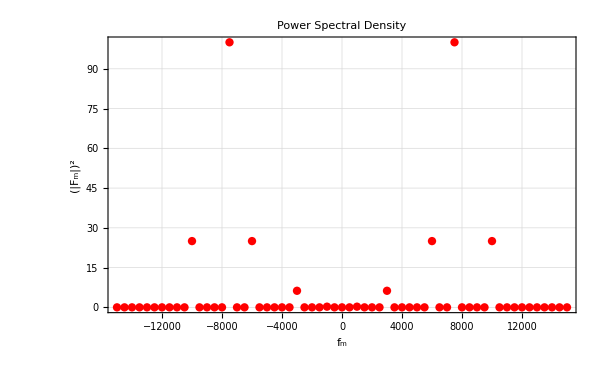

```mathematica
(* Plot the power density spectrum. *)
PowerSpectral = Transpose[{fm, PowerDensity}];
Show[ListPlot[PowerSpectral, ImageSize->{600, 400}, PlotStyle->{Directive[PointSize[0.01], Red]}, FrameLabel->{Style["f_m", Italic], Style[Superscript["|F_m|", 2], Italic]}, PlotLabel->"Power Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0],  Bold, FontSize->14, FontFamily->"Times"} , Frame->True]]
```

```mathematica
(* Check for Parseval's theorem. *)
Print[Style["Calculation of total average power using f(t):", Bold, FontFamily->"Times", FontSize->14]]
Pf1 = NIntegrate[Abs[f]^2, {t, -Tp/2, Tp/2}]/Tp
Print[Style["Calculation of total average power using F_m:", Bold, FontFamily->"Times", FontSize->14]]
Pf2 = Total[FmMagnitude^2]
```

Calculation of total average power using f(t):

313.

Calculation of total average power using F_m:

313

The Parseval’s equality holds for this signal. It represents that the total average power in the periodic signal equals to the sum of the average powers in all the harmonics constructing the original signal.

## Problem 6

The reconstructed signal:

1/2 ⅇ^(-2000 ⅈ π t)+1/2 ⅇ^(2000 ⅈ π t)+5/2 ⅈ ⅇ^(-6000 ⅈ π t)-5/2 ⅈ ⅇ^(6000 ⅈ π t)+5 ⅇ^(-12000 ⅈ π t)+5 ⅇ^(12000 ⅈ π t)+10 ⅇ^(-15000 ⅈ π t)+10 ⅇ^(15000 ⅈ π t)+5 ⅈ ⅇ^(-20000 ⅈ π t)-5 ⅈ ⅇ^(20000 ⅈ π t)

Cos[2000 π t]+10 Cos[12000 π t]+20 Cos[15000 π t]+5 Cos[6000 π t-π/2]+10 Cos[20000 π t-π/2]

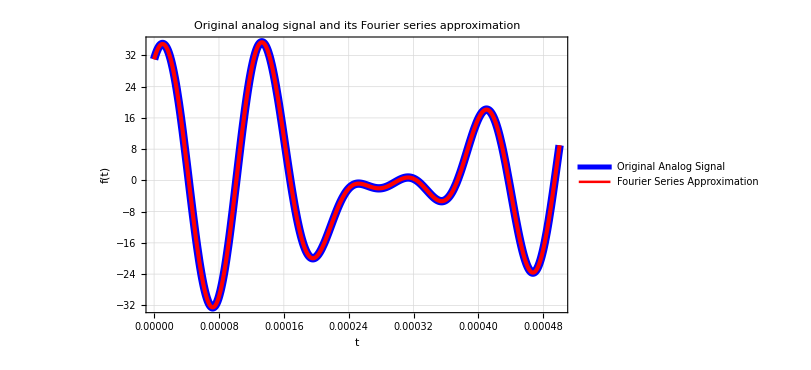

```mathematica
(* Calculate the reconstructed signal. *)
Print[Style["The reconstructed signal:", Bold, FontFamily->"Times", FontSize->14]]
ReconstructedSignal= Total[Fm*Exp[I*OmegaM*t]]
ExpToTrig[ReconstructedSignal]/.Sin[var_]:>HoldForm[Cos[var-π/2]]

(* Plot the original analog signal and the reconstructed signal. *)
Show[Plot[f, {t, 0, 0.0005}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.01]}, PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Original analog signal and its Fourier series approximation", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[ReconstructedSignal, {t, 0, 0.0005}, PlotStyle->{Red, Thickness[0.005]}, PlotLegends->{Style["Fourier Series Approximation", Bold, FontSize->14, FontFamily->"Times"]}]]
```

## Problem 7

The aperiodic function:

Piecewise[{{0, t<0}, {Cos[2000 π t]+10 Cos[12000 π t]+20 Cos[15000 π t]+5 Sin[6000 π t]+10 Sin[20000 π t], 0≤t≤0.002}, {0, True}}]

The Fourier coefficient:

(0.159155 ⅇ^((0.-0.0125664 ⅈ) k) (-1.+ⅇ^((0.+0.0125664 ⅈ) k)) (-4.86×10^33-(0.+2.97675×10^30 ⅈ) k+5.31428×10^27 k^2+(0.+1.62479×10^24 ⅈ) k^3-4.67284×10^20 k^4-(0.+1.84325×10^17 ⅈ) k^5+1.31238×10^13 k^6+(0.+4.78375×10^9 ⅈ) k^7-115000. k^8-(0.+31. ⅈ) k^9))/((-1.×10^8+k^2) (-5.625×10^7+k^2) (-3.6×10^7+k^2) (-9.×10^6+k^2) (-1.×10^6+k^2))

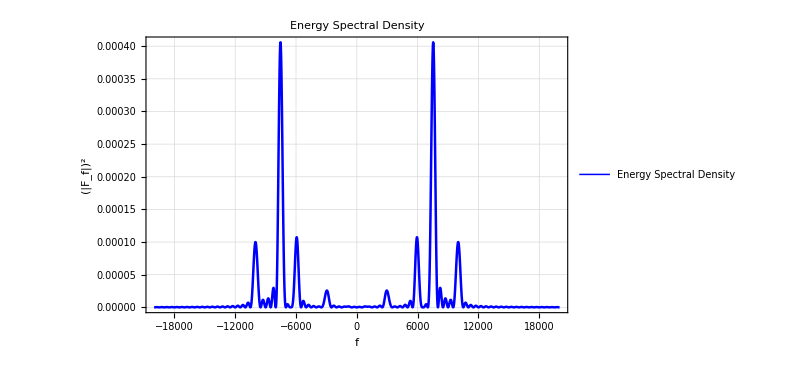

```mathematica
(*  Clear all the previous variables. *)
ClearAll["Global`*"];

(* Define the aperiodic function. *)
Print[Style["The aperiodic function:", Bold, FontFamily->"Times", FontSize->14]]
f= Piecewise[{{0, t<0}, {Cos[2000π t]+5Sin[6000π t]+10 Cos[12000 π t]+20Cos[15000π t]+10Sin[20000π t], 0<=t<=0.002}, {0, t>0.002}}]

(* Calculate the Fourier coefficient. *)
Print[Style["The Fourier coefficient:", Bold, FontFamily->"Times", FontSize->14]]
F = Integrate[f*Exp[-I*2π*k*t], {t, 0, 0.002}]
F2 = NIntegrate[f*Exp[-I*2π*k*t], {t, 0, 0.002}];

(* Calculate engergy and phase spectrum. *)
EnergySpectralDensity = Abs[F2]^2;
PhaseSpectralDensity= Arg[F2];

(* Plot the power density spectrum. *)
Show[Plot[EnergySpectralDensity, {k, -20000, 20000}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.003]}, PlotRange->All,PlotLegends->{Style["Energy Spectral Density", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["f", Italic], Style[Superscript["|F_f|", 2], Italic]}, PlotLabel->"Energy Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True]]

(* Plot the phase spectrum. *)
Show[Plot[PhaseSpectralDensity, {k, -20000, 20000}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.003]}, PlotRange->All,PlotLegends->{Style["Phase Spectral Density", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["f", Italic], Style[θ, Italic]}, PlotLabel->"Phase Spectral Density", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True]]
```

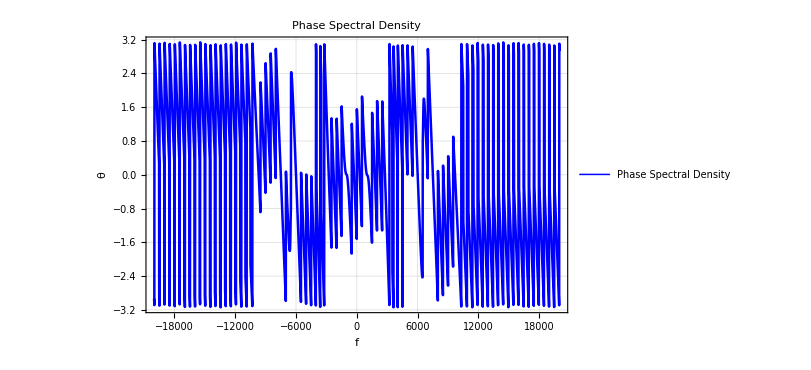

## Problem 8

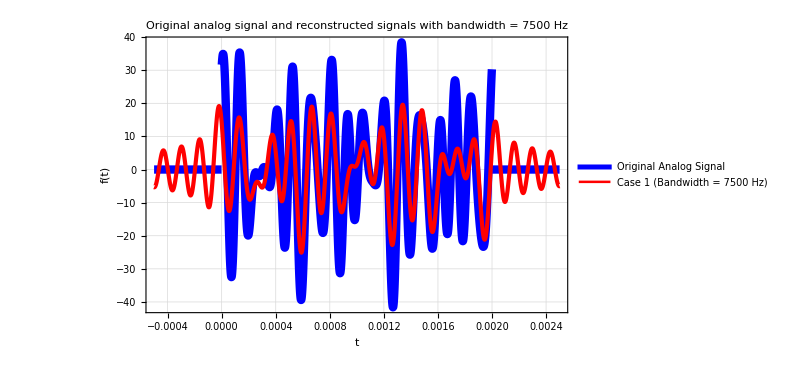

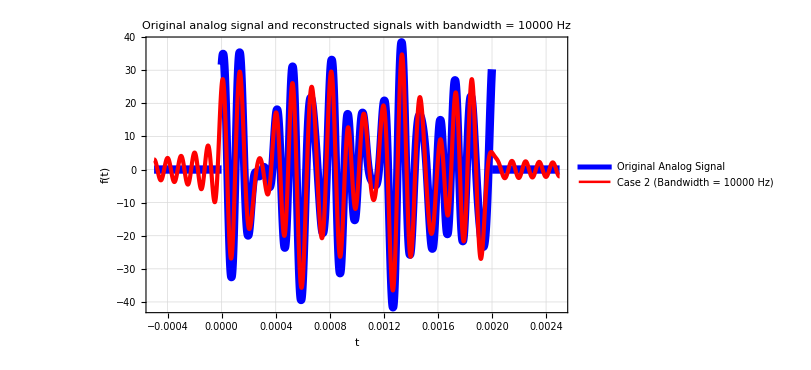

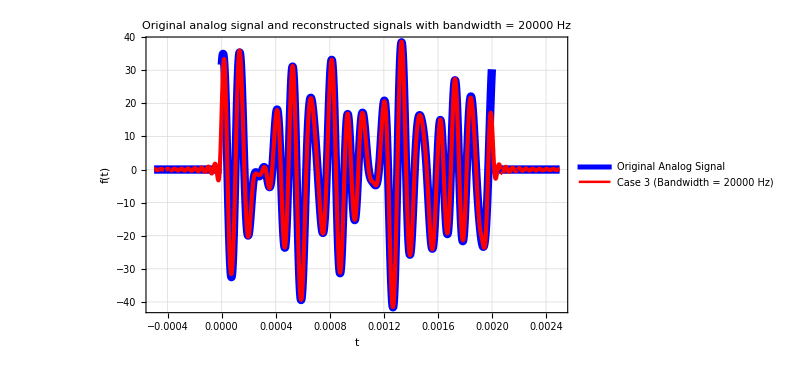

```mathematica
(* Calculate the reconstructed signal. *)
ReconstructedSignal1= NIntegrate[F*Exp[I*2π*k*t], {k, -7500, 7500}];
ReconstructedSignal2= NIntegrate[F*Exp[I*2π*k*t], {k, -10000, 10000}];
ReconstructedSignal3= NIntegrate[F*Exp[I*2π*k*t], {k, -20000, 20000}];

(* Plot the original analog signal and the reconstructed signals. *)
Show[Plot[f, {t, -0.0005, 0.0025}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.01]}, PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Original analog signal and reconstructed signals with bandwidth = 7500 Hz", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[ReconstructedSignal1, {t, -0.0005, 0.0025},PlotStyle->{Red, Thickness[0.005]}, PlotLegends->{Style["Case 1 (Bandwidth = 7500 Hz)", Bold, FontSize->14, FontFamily->"Times"]}]]

Show[Plot[f, {t, -0.0005, 0.0025}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.01]}, PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Original analog signal and reconstructed signals with bandwidth = 10000 Hz", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[ReconstructedSignal2, {t, -0.0005, 0.0025},PlotStyle->{Red, Thickness[0.005]}, PlotLegends->{Style["Case 2 (Bandwidth = 10000 Hz)", Bold, FontSize->14, FontFamily->"Times"]}]]

Show[Plot[f, {t, -0.0005, 0.0025}, ImageSize->{600, 400}, PlotStyle->{Blue, Thickness[0.01]}, PlotLegends->{Style["Original Analog Signal", Bold, FontSize->14, FontFamily->"Times"]},FrameLabel->{Style["t", Italic], Style["f(t)", Italic]}, PlotLabel->"Original analog signal and reconstructed signals with bandwidth = 20000 Hz", GridLines->Automatic, LabelStyle->{RGBColor[0,0,0], Bold, FontSize->14, FontFamily->"Times"}, Frame->True],
Plot[ReconstructedSignal3, {t, -0.0005, 0.0025},PlotStyle->{Red, Thickness[0.005]}, PlotLegends->{Style["Case 3 (Bandwidth = 20000 Hz)", Bold, FontSize->14, FontFamily->"Times"]}]]
```

As the bandwidth of frequency increases, more frequency components are included in the reconstruction and the reconstructed signal is closer to the original analog signal. However, because the original analog signal is not continuous, small vibration is observed outside the region between 0 and 0.002 second (Gibbs phenomenon).